```mathematica
filesAR=FileNames["/home/carla/GDC/PHI/GDC_Conf_AR_PHI_DOJ_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/PHI/GDC_Conf_BR_PHI_DOJ_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{0.000381136,15,39356},{0.00473934,1,211},{0.030303,5,165},{0.0104167,5,480},{0.00157978,5,3165},{0.00473934,5,1055},{1.,1,1}}

{{0.000381136,15,39356},{0.00473934,101,21311},{0.0108333,78,7200},{0.00156593,1300,830175},{0.00157978,5,3165},{0.00483092,1,207}}

```mathematica
dojAR=confAR[[All,1]]
dojBR=confBR[[All,1]]
```

{0.000381136,0.00473934,0.030303,0.0104167,0.00157978,0.00473934,1.}

{0.000381136,0.00473934,0.0108333,0.00156593,0.00157978,0.00483092}

```mathematica
sList={2,3,4,5,6,7,8};
sList2={2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
```

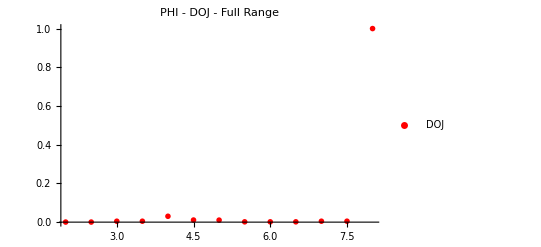

```mathematica
PlotDOJAllParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"PHI - DOJ - Full Range", PlotMarkers->{{"D",12}}]
```

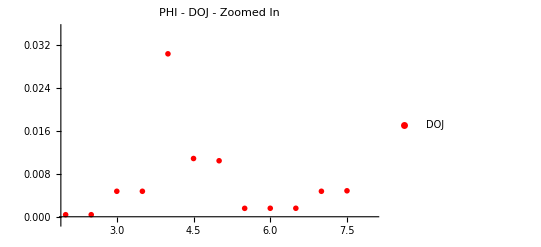

```mathematica
PlotDOJParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->{-0.001, 0.035},  PlotLabel->"PHI - DOJ - Zoomed In",  PlotMarkers->{{"D",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/PHI/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"PHI_DOJ.txt"]
Export["PHI_DOJ.jpeg",PlotDOJAllParts,ImageSize->850]
Export["PHI_DOJ_Zoomed_In.jpeg",PlotDOJParts,ImageSize->850]
```

PHI_DOJ.jpeg

PHI_DOJ_Zoomed_In.jpeg